```mathematica
SetDirectory[NotebookDirectory[]];
aRange={{-10,25},Full};
g[x_]:=PDF[NormalDistribution[5,5],x]
gActual=Rotate[Plot[g[x],{x,-10,25},Frame->{True,True,False,False},FrameTicks->{False,False,False,False},FrameLabel->{"θ",Rotate["p(θ|data)",Pi]},PlotStyle->Orange,PlotRange->aRange,Axes->None],Pi/2];
fProposal[θ_,σ_]:=RandomVariate[NormalDistribution[θ,σ],{1}][[1]]
fSingleStepMetropolis[θ_,σ_,aF_]:=Module[{aProposedTheta=fProposal[θ,σ],aRand=RandomReal[]},If[aF[aProposedTheta]>aF[θ],aProposedTheta,If[aRand<aF[aProposedTheta]/aF[θ],aProposedTheta,θ]]]
fStepMetropolis[nSteps_,aStart_,σ_,aF_]:=NestList[fSingleStepMetropolis[#,σ,aF]&,aStart,nSteps]
```

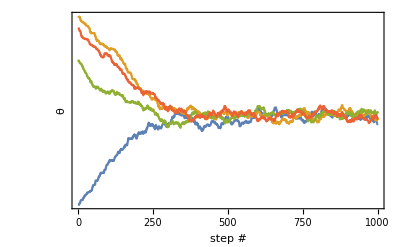

```mathematica
n = 1000;
lSamples1 = fStepMetropolis[n,RandomVariate[NormalDistribution[5,100],{1}][[1]],1,g];
lSamples2 = fStepMetropolis[n,RandomVariate[NormalDistribution[5,100],{1}][[1]],1,g];
lSamples3 = fStepMetropolis[n,RandomVariate[NormalDistribution[5,100],{1}][[1]],1,g];
lSamples4 = fStepMetropolis[n,RandomVariate[NormalDistribution[5,100],{1}][[1]],1,g];g1=ListLinePlot[{lSamples1,lSamples2,lSamples3,lSamples4},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,False,False,False},Axes->False,FrameLabel->{"step #","θ"},BaseStyle->{FontSize->14}]
```

```mathematica
fCalculateWithinChainVariance[lSamples__]:=Variance[lSamples]
fCalculateW[lSamplesAll__]:=Module[{m=Length@lSamplesAll,lWithin=fCalculateWithinChainVariance/@lSamplesAll},(Total@lWithin)/m]
fCalculateB[lSamplesAll__]:=Module[{m =Length@lSamplesAll,n=Length@lSamplesAll[[1]],lMeans=Mean/@lSamplesAll,aMeanTotal=Mean@Flatten[lSamplesAll]},(n/(m-1))Total@((lMeans-aMeanTotal)^2)]
fCalculateRhat[lSamplesAll__]:=Module[{W=fCalculateW[lSamplesAll],B=fCalculateB[lSamplesAll],n=Length@lSamplesAll[[1]],aNumerator},aNumerator=((n-1)/n)W + (1/n)B; Sqrt[aNumerator/W]]
```

```mathematica
lSamplesAll = Transpose@Thread[{lSamples1,lSamples2,lSamples3,lSamples4}];
```

```mathematica
fCalculateRunningRhat[lSamplesAll__]:=ParallelTable[fCalculateRhat[Transpose@(Transpose@lSamplesAll)[[1;;(i+1)]]],{i,1,Length@Transpose@lSamplesAll-2}]
```

```mathematica
fCalculateRunningW[lSamplesAll__]:=ParallelTable[fCalculateW[Transpose@(Transpose@lSamplesAll)[[1;;(i+1)]]],{i,1,Length@Transpose@lSamplesAll-2}]
fCalculateRunningB[lSamplesAll__]:=ParallelTable[fCalculateB[Transpose@(Transpose@lSamplesAll)[[1;;(i+1)]]],{i,1,Length@Transpose@lSamplesAll-2}]
```

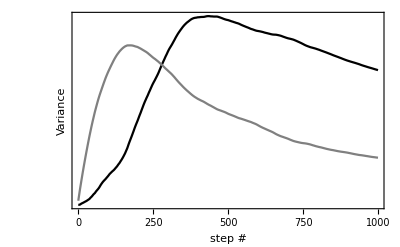

```mathematica
g2=ListLinePlot[{(1-(1/1000))fCalculateRunningW[lSamplesAll],(1/1000)fCalculateRunningB[lSamplesAll]},PlotRange->{Automatic,Automatic},PlotStyle->{Black,Gray},Frame->{True,True,False,False},FrameTicks->{True,False,False,False},Axes->False,FrameLabel->{"step #","Variance"},BaseStyle->{FontSize->14}]
```

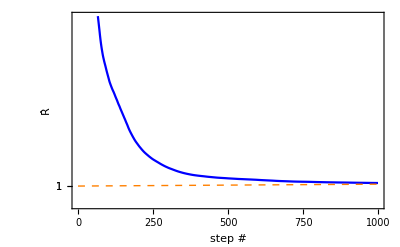

```mathematica
yTicks={1,1};
g3=ListLinePlot[fCalculateRunningRhat[lSamplesAll],PlotRange->{Automatic,{0,10}},PlotStyle->Blue,Epilog->{Dashed,Orange,Line[{{0,1},{1000,1.1}}]},Frame->{True,True,False,False},FrameTicks->{True,yTicks,False,False},Axes->False,FrameLabel->{"step #","R̂"},BaseStyle->{FontSize->14}]
```

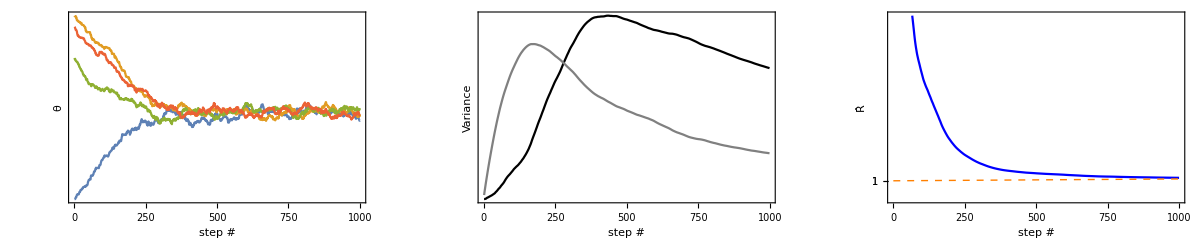

```mathematica
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->1200]
```

```mathematica
Export["metropolisHastings_warmUp.pdf",gFinal]
```

metropolisHastings_warmUp.pdf